```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

Energy equivalence hypothesis

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

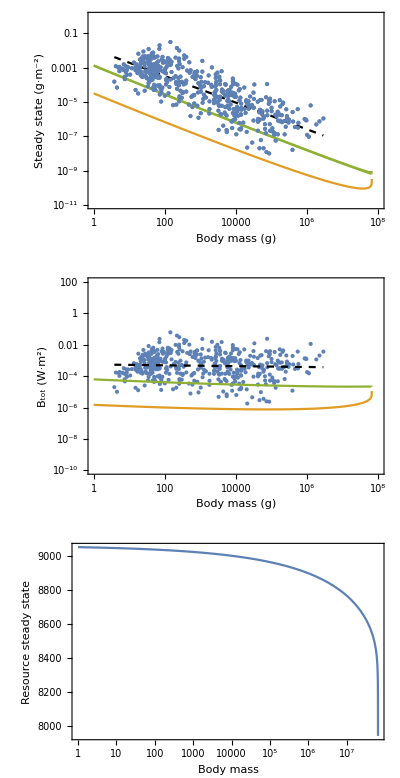

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,1,10^8},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,1,10^8},Frame->True,PlotRange->All,FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

```mathematica
NIntegrate[(1/M)*(dimF/M*M^(3/4)*B0),{M,10^3,10^5}]
```

0.000132489

```mathematica
FindMaximum[Re[HFM[[1]]],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.59227,{M→6.53794×10^7}}

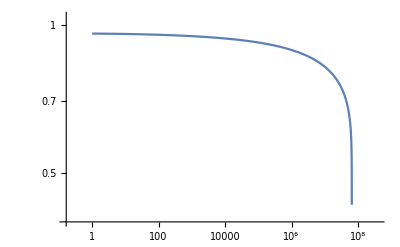

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^9},PlotRange->All]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}